Test for Toptica DL pro laser divergence/beam defects with no optics modifications. Used thorlabs _______ and marked the top and right most edge, than turned dials till the marking reached opposite side and took measurements. Each dot had a radius of around .02” and put center of dot on edge, so each measurement has an uncertainty of around .02” from dot and .0005” from dials, so we will just say .02”. The distance from the laser is measured from base of DL Pro aperture, the uncertainty increases as the bend of tape measure increase as it gets longer. 

The overall shape of the laser appears oval like with longest edges in horizontal/x direction (at first). over distance this actually switches to the longest being vertical/z direction. This is based on the brightest point of laser seen on camera, but only the brightest part is what we can see visually not using my iPhone 14 camera 1x zoom, each picture was taken from 8 1/2” away. Look bellow to see.

### Beam Size Data

```mathematica
(* Sample Data *)
data = {
  {{8.5625, .0625}, {0.154, 0.02}, {0.064, 0.02}, {3.881, 0.02}},  (* Trial 1 *)
  {{75.5, .25}, {0.157, 0.02}, {0.081, 0.02}, {3.907, 0.02}}, (* Trial 2 *)
  {{141.5, 0.5}, {0.123, 0.02}, {0.130, 0.02}, {3.928, 0.02}}, (* Trial 3 *)
  {{248, 1}, {0.134, 0.02}, {0.195, 0.02}, {Null, Null}}  (* Trial 4 *)
};

(* Add row labels *)
labeledData = Prepend[
  MapIndexed[Prepend[#1 /. {x_, y_} :> Row[{x, " ± ", y}], "Trial " <> ToString[First[#2]]] &, data],
  {"", "Distance y", "Width Beam, Δx", "Heigth Beam, Δz", "Height From Table, z"} (* Header Row *)
];

(* Displaying the Data in a Grid *)
Grid[
  labeledData,
  Frame -> All
]
```

| Distance y | Width Beam, Δx | Heigth Beam, Δz | Height From Table, z
Trial 1 | 8.5625 ± 0.0625 | 0.154 ± 0.02 | 0.064 ± 0.02 | 3.881 ± 0.02
Trial 2 | 75.5 ± 0.25 | 0.157 ± 0.02 | 0.081 ± 0.02 | 3.907 ± 0.02
Trial 3 | 141.5 ± 0.5 | 0.123 ± 0.02 | 0.13 ± 0.02 | 3.928 ± 0.02
Trial 4 | 248 ± 1 | 0.134 ± 0.02 | 0.195 ± 0.02 |  ±

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

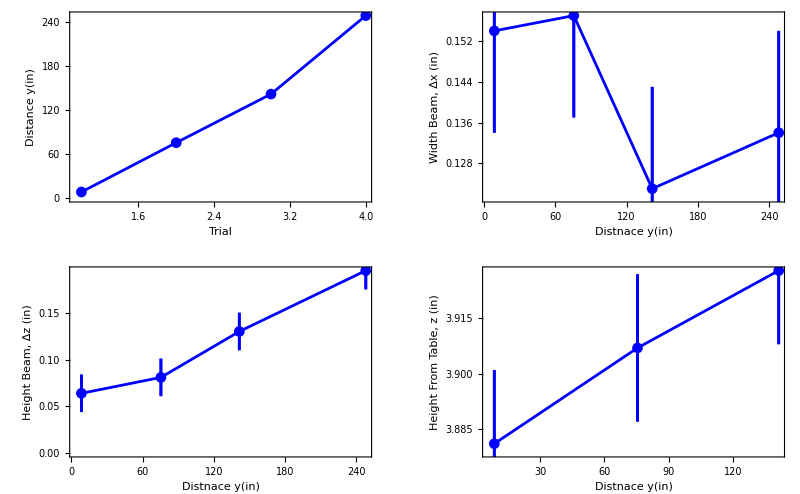

```mathematica
Needs["ErrorBarPlots`"]

(* Sample Data *)
data = {
  {{8.5625, .0625}, {0.154, 0.02}, {0.064, 0.02}, {3.881, 0.02}},  (* Trial 1 *)
  {{75.5, .25}, {0.157, 0.02}, {0.081, 0.02}, {3.907, 0.02}},     (* Trial 2 *)
  {{141.5, 0.5}, {0.123, 0.02}, {0.130, 0.02}, {3.928, 0.02}},     (* Trial 3 *)
  {{248, 1}, {0.134, 0.02}, {0.195, 0.02}, {Null, Null}}                (* Trial 4 *)
};

(* Function to clean data and remove Null values *)
cleanData[measurement_] := Select[measurement, #[[1]] =!= Null &]

(* Extracting each measurement type and cleaning the data *)
distanceY = cleanData[data[[All, 1]]];      (* Distance y *)
widthBeam = cleanData[data[[All, 2]]];      (* Width Beam, Δx *)
heightBeam = cleanData[data[[All, 3]]];     (* Height Beam, Δz *)
heightFromTable = cleanData[data[[All, 4]]]; (* Height From Table, z *)

(* Combine measurmnets to make functions of distnaceY*)
widthBeam2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {widthBeam, distanceY}];
heightBeam2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {heightBeam, distanceY}];
heightFromTable2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {heightFromTable, Drop[distanceY,-1]}];

(* Function to create simple plots *)
createSimplePlot[measurement_, y_,x_] := ErrorListPlot[
  measurement,
  PlotMarkers -> Automatic,
  PlotStyle -> Blue,
  PlotRange -> All,
  Frame -> True,
  FrameLabel -> {x, y},
  Joined -> True
];

(* Generating plots *)
distanceYPlot = createSimplePlot[distanceY, "Distance y(in)","Trial"];
widthBeamPlot = createSimplePlot[widthBeam2, "Width Beam, Δx (in)","Distnace y(in)"];
heightBeamPlot = createSimplePlot[heightBeam2, "Height Beam, Δz (in)","Distnace y(in)"];
heightFromTablePlot = createSimplePlot[heightFromTable2, "Height From Table, z (in)","Distnace y(in)"];

(* Display all plots together *)
GraphicsGrid[{
  {distanceYPlot, widthBeamPlot},
  {heightBeamPlot, heightFromTablePlot}
}]
```

Slope: 0.0501263

Uncertainty in Slope: 0.00918846

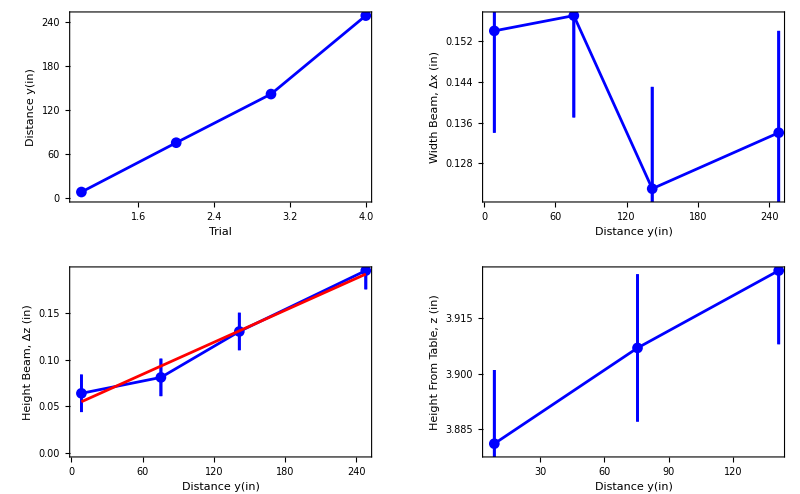

```mathematica
Needs["ErrorBarPlots`"]

(* Sample Data *)
data = {
  {{8.5625, .0625}, {0.154, 0.02}, {0.064, 0.02}, {3.881, 0.02}},  (* Trial 1 *)
  {{75.5, .25}, {0.157, 0.02}, {0.081, 0.02}, {3.907, 0.02}},     (* Trial 2 *)
  {{141.5, 0.5}, {0.123, 0.02}, {0.130, 0.02}, {3.928, 0.02}},     (* Trial 3 *)
  {{248, 1}, {0.134, 0.02}, {0.195, 0.02}, {Null, Null}}                (* Trial 4 *)
};

(* Function to clean data and remove Null values *)
cleanData[measurement_] := Select[measurement, #[[1]] =!= Null &]

(* Extracting each measurement type and cleaning the data *)
distanceY = cleanData[data[[All, 1]]];      (* Distance y *)
widthBeam = cleanData[data[[All, 2]]];      (* Width Beam, Δx *)
heightBeam = cleanData[data[[All, 3]]];     (* Height Beam, Δz *)
heightFromTable = cleanData[data[[All, 4]]]; (* Height From Table, z *)

(* Combine measurements to make functions of distanceY *)
widthBeam2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {widthBeam, distanceY}];
heightBeam2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {heightBeam, distanceY}];
heightFromTable2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {heightFromTable, Drop[distanceY, -1]}];

(* Function to create simple plots *)
createSimplePlot[measurement_, y_, x_] := ErrorListPlot[
  measurement,
  PlotMarkers -> Automatic,
  PlotStyle -> Blue,
  PlotRange -> All,
  Frame -> True,
  FrameLabel -> {x, y},
  Joined -> True
];

(* Extracting x and y values from heightBeam2 for linear fit *)
xVals = heightBeam2[[All, 1, 1]];
yVals = heightBeam2[[All, 1, 2]];

(* Perform the linear fit using LinearModelFit *)
linearModel = LinearModelFit[Transpose[{xVals, yVals}], x, x];

(* Extract the slope and its uncertainty *)
slope = linearModel["BestFitParameters"][[1]];
slopeUncertainty = linearModel["ParameterErrors"][[1]];

(* Print the slope and its uncertainty *)
Print["Slope: ", slope];
Print["Uncertainty in Slope: ", slopeUncertainty];

(* Generating plots *)
distanceYPlot = createSimplePlot[distanceY, "Distance y(in)", "Trial"];
widthBeamPlot = createSimplePlot[widthBeam2, "Width Beam, Δx (in)", "Distance y(in)"];
heightBeamPlot = Show[
  createSimplePlot[heightBeam2, "Height Beam, Δz (in)", "Distance y(in)"],
  Plot[linearModel[x], {x, Min[xVals], Max[xVals]}, PlotStyle -> Red]
];
heightFromTablePlot = createSimplePlot[heightFromTable2, "Height From Table, z (in)", "Distance y(in)"];

(* Display all plots together *)
GraphicsGrid[{
  {distanceYPlot, widthBeamPlot},
  {heightBeamPlot, heightFromTablePlot}
}]
```

Slope for Width Beam Plot: -0.000110047

Divergence Angle for Width Beam Plot: -0.00630521

Slope for Height Beam Plot: 0.00056908

Divergence Angle for Height Beam Plot: 0.0326059

Slope for Height From Table Plot: 0.000353632

Divergence Angle for Height From Table Plot: 0.0202616

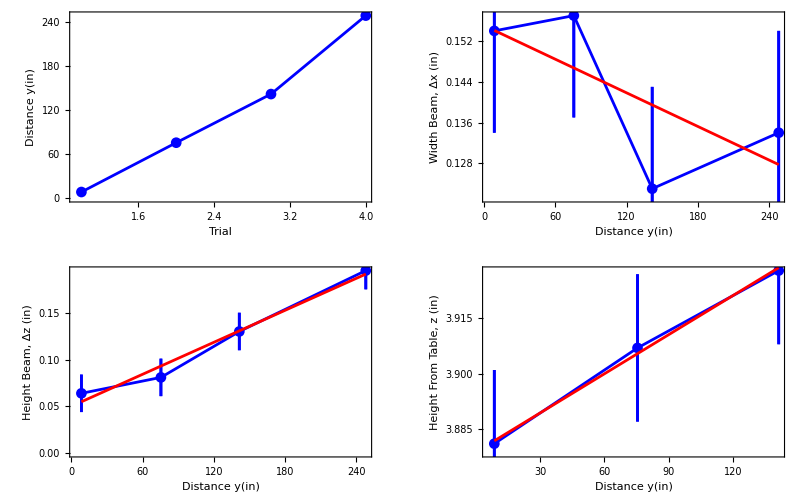

```mathematica
Needs["ErrorBarPlots`"]

(* Sample Data *)
data = {
  {{8.5625, .0625}, {0.154, 0.02}, {0.064, 0.02}, {3.881, 0.02}},  (* Trial 1 *)
  {{75.5, .25}, {0.157, 0.02}, {0.081, 0.02}, {3.907, 0.02}},     (* Trial 2 *)
  {{141.5, 0.5}, {0.123, 0.02}, {0.130, 0.02}, {3.928, 0.02}},     (* Trial 3 *)
  {{248, 1}, {0.134, 0.02}, {0.195, 0.02}, {Null, Null}}                (* Trial 4 *)
};

(* Function to clean data and remove Null values *)
cleanData[measurement_] := Select[measurement, #[[1]] =!= Null &]

(* Extracting each measurement type and cleaning the data *)
distanceY = cleanData[data[[All, 1]]];      (* Distance y *)
widthBeam = cleanData[data[[All, 2]]];      (* Width Beam, Δx *)
heightBeam = cleanData[data[[All, 3]]];     (* Height Beam, Δz *)
heightFromTable = cleanData[data[[All, 4]]]; (* Height From Table, z *)

(* Combine measurements to make functions of distanceY *)
widthBeam2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {widthBeam, distanceY}];
heightBeam2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {heightBeam, distanceY}];
heightFromTable2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {heightFromTable, Drop[distanceY, -1]}];

(* Function to create simple plots *)
createSimplePlot[measurement_, y_, x_] := ErrorListPlot[
  measurement,
  PlotMarkers -> Automatic,
  PlotStyle -> Blue,
  PlotRange -> All,
  Frame -> True,
  FrameLabel -> {x, y},
  Joined -> True
];

(* Function to perform linear fit, plot, and print slope/uncertainty *)
linearFitPlot[measurementData_, yLabel_, xLabel_, plotName_] := Module[
  {xVals, yVals, linearModel, slope, slopeUncertainty},
  
  (* Extract x and y values from the measurement data *)
  xVals = measurementData[[All, 1, 1]];
  yVals = measurementData[[All, 1, 2]];
  
  (* Perform the linear fit using LinearModelFit *)
  linearModel = LinearModelFit[Transpose[{xVals, yVals}], x, x];
  
  (* Extract the slope and its uncertainty *)
  slope = linearModel["BestFitParameters"][[2]];
  slopeUncertainty = linearModel["ParameterErrors"][[2]];
  
  (* Print the slope and its uncertainty with a descriptive label *)
 Print["Slope for ", plotName, ": ", slope];
 (* Print["Uncertainty in Slope for ", plotName, ": ", slopeUncertainty];*);
  Print["Divergence Angle for ", plotName, ": ", ArcTan[slope]/Degree];
  
  (* Create and return the plot with the linear fit *)
  Show[
    createSimplePlot[measurementData, yLabel, xLabel],
    Plot[linearModel[x], {x, Min[xVals], Max[xVals]}, PlotStyle -> Red]
  ]
];

(* Generating plots using the linearFitPlot function *)
distanceYPlot = createSimplePlot[distanceY, "Distance y(in)", "Trial"];
widthBeamPlot = linearFitPlot[widthBeam2, "Width Beam, Δx (in)", "Distance y(in)", "Width Beam Plot"];
heightBeamPlot = linearFitPlot[heightBeam2, "Height Beam, Δz (in)", "Distance y(in)", "Height Beam Plot"];
heightFromTablePlot = linearFitPlot[heightFromTable2, "Height From Table, z (in)", "Distance y(in)", "Height From Table Plot"];

(* Display all plots together *)
GraphicsGrid[{
  {distanceYPlot, widthBeamPlot},
  {heightBeamPlot, heightFromTablePlot}
}]
```

```mathematica
Needs["ErrorBarPlots`"]

(* Sample Data *)
data = {
  {{8.5625, .0625}, {0.154, 0.02}, {0.064, 0.02}, {3.881, 0.02}},  (* Trial 1 *)
  {{75.5, .25}, {0.157, 0.02}, {0.081, 0.02}, {3.907, 0.02}},     (* Trial 2 *)
  {{141.5, 0.5}, {0.123, 0.02}, {0.130, 0.02}, {3.928, 0.02}},     (* Trial 3 *)
  {{248, 1}, {0.134, 0.02}, {0.195, 0.02}, {Null, Null}}                (* Trial 4 *)
};

(* Function to clean data and remove Null values *)
cleanData[measurement_] := Select[measurement, #[[1]] =!= Null &]

(* Extracting each measurement type and cleaning the data *)
distanceY = cleanData[data[[All, 1]]];      (* Distance y *)
widthBeam = cleanData[data[[All, 2]]];      (* Width Beam, Δx *)
heightBeam = cleanData[data[[All, 3]]];     (* Height Beam, Δz *)
heightFromTable = cleanData[data[[All, 4]]]; (* Height From Table, z *)

(* Combine measurements to make functions of distanceY *)
widthBeam2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {widthBeam, distanceY}];
heightBeam2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {heightBeam, distanceY}];
heightFromTable2 = MapThread[{{#2[[1]], #1[[1]]}, ErrorBar[#1[[2]]]} &, {heightFromTable, Drop[distanceY, -1]}];

(* Function to create simple plots *)
createSimplePlot[measurement_, y_, x_] := ErrorListPlot[
  measurement,
  PlotMarkers -> Automatic,
  PlotStyle -> Blue,
  PlotRange -> All,
  Frame -> True,
  FrameLabel -> {x, y},
  Joined -> True
];

(* Function to perform linear fit, plot, and print slope/uncertainty *)
linearFitPlot[measurementData_, yLabel_, xLabel_, plotName_] := Module[
  {xVals, yVals, linearModel, slope, intercept, slopeUncertainty, equation},
  
  (* Extract x and y values from the measurement data *)
  xVals = measurementData[[All, 1, 1]];
  yVals = measurementData[[All, 1, 2]];
  
  (* Perform the linear fit using LinearModelFit *)
  linearModel = LinearModelFit[Transpose[{xVals, yVals}], x, x];
  
  (* Extract the slope, intercept, and their uncertainties *)
  intercept = linearModel["BestFitParameters"][[1]]; (* Intercept is the first parameter *)
  slope = linearModel["BestFitParameters"][[2]];     (* Slope is the second parameter *)
  slopeUncertainty = linearModel["ParameterErrors"][[2]]; (* Uncertainty for slope *)
  
  (* Create the equation string *)
  equation = "y = " <> ToString[slope] <> " x + " <> ToString[intercept];
  
  (* Print the equation and the uncertainty with a descriptive label *)
  Print["Best Fit Equation for ", plotName, ": ", equation];
  Print["Uncertainty in Slope for ", plotName, ": ", slopeUncertainty];
  Print["Divergence Angle for ", plotName, ": ", Style[ArcTan[slope]/Degree, Underlined]];
  (* Create and return the plot with the linear fit *)
  Show[
    createSimplePlot[measurementData, yLabel, xLabel],
    Plot[linearModel[x], {x, Min[xVals], Max[xVals]}, PlotStyle -> Red]
  ]
];

(* Generating plots using the linearFitPlot function *)
distanceYPlot = createSimplePlot[distanceY, "Distance y(in)", "Trial"];
widthBeamPlot = linearFitPlot[widthBeam2, "Width Beam, Δx (in)", "Distance y(in)", "Width Beam Plot"];
heightBeamPlot = linearFitPlot[heightBeam2, "Height Beam, Δz (in)", "Distance y(in)", "Height Beam Plot"];
heightFromTablePlot = linearFitPlot[heightFromTable2, "Height From Table, z (in)", "Distance y(in)", "Height From Table Plot"];

(* Display all plots together *)
GraphicsGrid[{
  {distanceYPlot, widthBeamPlot},
  {heightBeamPlot, heightFromTablePlot}
}]
```

Best Fit Equation for Width Beam Plot: y = -0.000110047 x + 0.155029

Uncertainty in Slope for Width Beam Plot: 0.0000815793

Divergence Angle for Width Beam Plot: -0.00630521

Best Fit Equation for Height Beam Plot: y = 0.00056908 x + 0.0501263

Uncertainty in Slope for Height Beam Plot: 0.0000621965

Divergence Angle for Height Beam Plot: 0.0326059

Best Fit Equation for Height From Table Plot: y = 0.000353632 x + 3.87874

Uncertainty in Slope for Height From Table Plot: 0.0000202753

Divergence Angle for Height From Table Plot: 0.0202616

-Graphics-